```mathematica
SetDirectory[$UserDocumentsDirectory<>"/Github/covidmodel"];
Import["model/autoindent.wl"];
Autoindent["model/model.wl"];
Autoindent["model/data.wl"];
Autoindent["model/gof-metrics.wl"];
```

```mathematica
SetDirectory[$UserDocumentsDirectory<>"/Github/covidmodel"];
Import["model/model.wl"]
```

Fitting model for CA

>> <|chiSquared→0.0000139862,rmsRelativeError→0.872514,rmsRelativeErrorDeaths→0.767369,rmsRelativeErrorPcr→0.951606,meanRelativeErrorDeaths→-0.600683,meanRelativeErrorPcr→-0.439569,rSquaredDeaths→0.0389981,rSquaredPcr→0.0581149,deathResidual7Day→-1.39218,pcrResidual7Day→42.0069|>

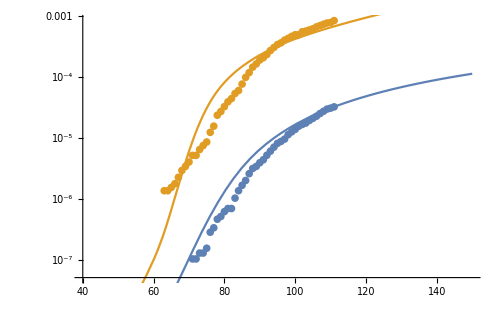
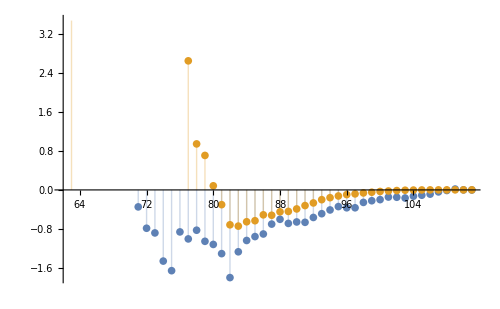
>> Fit for CA
-Graphics--Graphics-
 | Estimate | Standard Error | t-Statistic | P-Value
ⅇ^r0natural | 4.39858 | 0.279683 | 15.727 | HypothesisTesting`TwoSidedPValue/.HypothesisTesting`StudentTPValue[15.727,86.,HypothesisTesting`TwoSided→True]
ⅇ^importtime | 38.1359 | 2.29035 | 16.6507 | HypothesisTesting`TwoSidedPValue/.HypothesisTesting`StudentTPValue[16.6507,86.,HypothesisTesting`TwoSided→True]
ⅇ^stateAdjustmentForTestingDifferences | 0.716923 | 0.0706721 | 10.1444 | HypothesisTesting`TwoSidedPValue/.HypothesisTesting`StudentTPValue[10.1444,86.,HypothesisTesting`TwoSided→True]
ⅇ^distpow | 1.90856 | 0.233891 | 8.16004 | HypothesisTesting`TwoSidedPValue/.HypothesisTesting`StudentTPValue[8.16004,86.,HypothesisTesting`TwoSided→True] | DF | SS | MS
Model | 4 | 3.38518×10^-9 | 8.46296×10^-10
Error | 86 | 2.5781×10^-10 | 2.99779×10^-12
Uncorrected Total | 90 | 3.64299×10^-9 | 
Corrected Total | 89 | 3.5953×10^-9 |

>> Current Indefinite scenario Generating simulations for CA in the

Part::partw: Part 1 of {} does not exist.

>> Current scenario Generating simulations for CA in the

>> Generating simulations for CA in the  Italy scenario

>> Generating simulations for CA in the  Wuhan scenario

>> Generating simulations for CA in the  Normal scenario

>> Generating simulations for CA in the  Open May 1 scenario

>> Generating simulations for CA in the  Open Gradual May 1 scenario

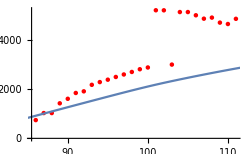
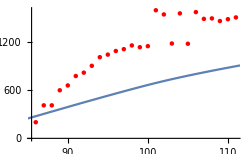
>> Current Hospitalizations for CA
-Graphics-Cumulative Hospitalizations for CA
-Graphics-Current ICU for CA
-Graphics-Cumulative ICU for CA
-Graphics-

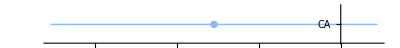
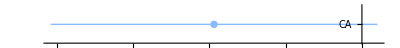
Currently Hospitalized
-Graphics- | Cumulative Hospitalized
-Graphics- | Currently ICU
-Graphics- | Cumulative ICU
-Graphics-

state | distancingLevel | id | distancingDays | maintain | name | gradual | summaryAug1 | totalProjectedDeaths | totalProjectedPCRConfirmed | totalProjectedInfected | totalInfectedFraction | fatalityRate | fatalityRateSymptomatic | fatalityRatePCR | fractionOfSymptomaticHospitalized | fractionOfSymptomaticHospitalizedOrICU | fractionOfPCRHospitalized | fractionOfPCRHospitalizedOrICU | fractionHospitalizedInICU | fractionOfDeathInICU | fractionDeathOfHospitalizedOrICU | fractionOfInfectionsPCRConfirmed | dateContained | dateICUOverCapacity | dateHospitalsOverCapacity | {"r0natural", "importtime", "stateAdjustmentForTestingDifferences"} |  |  | 
CA | 0.474762 | scenario5 | 618 | True | Current Indefinite | False | <|"totalProjectedDeaths" -> 10522.251170301823, "totalProjectedPCRConfirmed" -> 273630.25595533906, "totalProjectedInfected" -> 1.1171534012882118*^6, "totalInfectedFraction" -> 0.02865756319152913, "fatalityRate" -> 0.009418806010140062, "fatalityRateSymptomatic" -> 0.013455437157342948, "fatalityRatePCR" -> 0.03845426790822148, "fractionOfSymptomaticHospitalized" -> 0.06221300541848605, "fractionOfSymptomaticHospitalizedOrICU" -> 0.08524880961813652, "fractionOfPCRHospitalized" -> 0.17632500062465992, "fractionOfPCRHospitalizedOrICU" -> 0.24161341038031506, "fractionHospitalizedInICU" -> 0.2702184851945385, "fractionOfDeathInICU" -> 0.5469991262883751, "fractionDeathOfHospitalizedOrICU" -> 0.15915618196726738, "fractionOfInfectionsPCRConfirmed" -> 0.24493525744970263, "dateContained" -> "Thu 2 Jan 2020 00:00:00", "dateICUOverCapacity" -> "", "dateHospitalsOverCapacity" -> ""|> | 36361.8 | 923872. | 3.06861×10^6 | 0.0787169 | 0.0118496 | 0.016928 | 0.039358 | 0.0699392 | 0.0958357 | 0.18549 | 0.254171 | 0.270218 | 0.546128 | 0.154849 | 0.301072 | Thu 2 Jan 2020 00:00:00 |  |  | 4.39858 | 38.1359 | 0.716923 | 
CA | 0.474762 | scenario1 | 90 | True | Current | False | <|"totalProjectedDeaths" -> 10739.303240150555, "totalProjectedPCRConfirmed" -> 395124.99551868037, "totalProjectedInfected" -> 2.0837986607822012*^6, "totalInfectedFraction" -> 0.05345424516537238, "fatalityRate" -> 0.005153714436172694, "fatalityRateSymptomatic" -> 0.007362449194532419, "fatalityRatePCR" -> 0.0271795086667526, "fractionOfSymptomaticHospitalized" -> 0.03725303627943049, "fractionOfSymptomaticHospitalizedOrICU" -> 0.05104683459865528, "fractionOfPCRHospitalized" -> 0.1395537364010876, "fractionOfPCRHospitalizedOrICU" -> 0.1912267350842513, "fractionHospitalizedInICU" -> 0.2702184851945385, "fractionOfDeathInICU" -> 0.545404308902945, "fractionDeathOfHospitalizedOrICU" -> 0.14213236791799935, "fractionOfInfectionsPCRConfirmed" -> 0.18961764538727616, "dateContained" -> "Fri 27 Nov 2020 00:00:00", "dateICUOverCapacity" -> "Thu 6 Aug 2020 13:31:23", "dateHospitalsOverCapacity" -> "Sat 8 Aug 2020 11:39:14"|> | 380262. | 1.02896×10^7 | 3.20012×10^7 | 0.820906 | 0.0118827 | 0.0169753 | 0.0369559 | 0.0700301 | 0.0959604 | 0.183744 | 0.251779 | 0.270218 | 0.546206 | 0.146779 | 0.321539 | Fri 27 Nov 2020 00:00:00 | Thu 6 Aug 2020 13:31:23 | Sat 8 Aug 2020 11:39:14 | 4.39858 | 38.1359 | 0.716923 | 
CA | 0.2 | scenario2 | 90 | False | Italy | False | <|"totalProjectedDeaths" -> 3319.327229198863, "totalProjectedPCRConfirmed" -> 40936.687016987446, "totalProjectedInfected" -> 280268.16106093384, "totalInfectedFraction" -> 0.007189525204789015, "fatalityRate" -> 0.011843397468459499, "fatalityRateSymptomatic" -> 0.01691913924065643, "fatalityRatePCR" -> 0.08108441281096943, "fractionOfSymptomaticHospitalized" -> 0.07001451622084011, "fractionOfSymptomaticHospitalizedOrICU" -> 0.09593901023856975, "fractionOfPCRHospitalized" -> 0.20461141511443576, "fractionOfPCRHospitalizedOrICU" -> 0.2803735240799833, "fractionHospitalizedInICU" -> 0.27021848519453856, "fractionOfDeathInICU" -> 0.5451164680829359, "fractionDeathOfHospitalizedOrICU" -> 0.28920138974262827, "fractionOfInfectionsPCRConfirmed" -> 0.14606256687175856, "dateContained" -> "Sun 24 May 2020 00:00:00", "dateICUOverCapacity" -> "Thu 17 Sep 2020 08:02:04", "dateHospitalsOverCapacity" -> "Fri 18 Sep 2020 23:12:12"|> | 382212. | 1.03621×10^7 | 3.21653×10^7 | 0.825115 | 0.0118827 | 0.0169753 | 0.0368856 | 0.0700301 | 0.0959604 | 0.183639 | 0.251635 | 0.270218 | 0.546206 | 0.146584 | 0.322151 | Sun 24 May 2020 00:00:00 | Thu 17 Sep 2020 08:02:04 | Fri 18 Sep 2020 23:12:12 | 4.39858 | 38.1359 | 0.716923 | 
CA | 0.11 | scenario3 | 60 | False | Wuhan | False | <|"totalProjectedDeaths" -> 3311.3793863473466, "totalProjectedPCRConfirmed" -> 85083.84096405146, "totalProjectedInfected" -> 608069.4556541975, "totalInfectedFraction" -> 0.015598384993640857, "fatalityRate" -> 0.005445725575517958, "fatalityRateSymptomatic" -> 0.007779607965025656, "fatalityRatePCR" -> 0.03891901621773785, "fractionOfSymptomaticHospitalized" -> 0.036966975741690895, "fractionOfSymptomaticHospitalizedOrICU" -> 0.050654853530436736, "fractionOfPCRHospitalized" -> 0.12928219410987077, "fractionOfPCRHospitalizedOrICU" -> 0.17715191668609703, "fractionHospitalizedInICU" -> 0.27021848519453856, "fractionOfDeathInICU" -> 0.5430963143409429, "fractionDeathOfHospitalizedOrICU" -> 0.21969288814808646, "fractionOfInfectionsPCRConfirmed" -> 0.13992454344300712, "dateContained" -> "Mon 18 May 2020 00:00:00", "dateICUOverCapacity" -> "Wed 12 Aug 2020 06:44:36", "dateHospitalsOverCapacity" -> "Thu 13 Aug 2020 21:52:14"|> | 382253. | 1.03645×10^7 | 3.21687×10^7 | 0.825202 | 0.0118827 | 0.0169753 | 0.0368811 | 0.0700301 | 0.0959604 | 0.183634 | 0.251629 | 0.270218 | 0.546206 | 0.14657 | 0.32219 | Mon 18 May 2020 00:00:00 | Wed 12 Aug 2020 06:44:36 | Thu 13 Aug 2020 21:52:14 | 4.39858 | 38.1359 | 0.716923 | 
CA | 1 | scenario4 | 90 | False | Normal | False | <|"totalProjectedDeaths" -> 375017.3344162807, "totalProjectedPCRConfirmed" -> 9.105977340994194*^6, "totalProjectedInfected" -> 3.2177365265778698*^7, "totalInfectedFraction" -> 0.8254236861093983, "fatalityRate" -> 0.011654693643146707, "fatalityRateSymptomatic" -> 0.016649562347352438, "fatalityRatePCR" -> 0.04118364458562732, "fractionOfSymptomaticHospitalized" -> 0.06983524939851635, "fractionOfSymptomaticHospitalizedOrICU" -> 0.09569336572896397, "fractionOfPCRHospitalized" -> 0.19191135598916323, "fractionOfPCRHospitalizedOrICU" -> 0.26297097432006244, "fractionHospitalizedInICU" -> 0.2702184851945388, "fractionOfDeathInICU" -> 0.5476097403100125, "fractionDeathOfHospitalizedOrICU" -> 0.15660908848252825, "fractionOfInfectionsPCRConfirmed" -> 0.28299325522088636, "dateContained" -> "Sat 29 Aug 2020 00:00:00", "dateICUOverCapacity" -> "Sat 9 May 2020 15:55:31", "dateHospitalsOverCapacity" -> "Mon 11 May 2020 09:43:02"|> | 382437. | 9.11662×10^6 | 3.21843×10^7 | 0.8256 | 0.0118827 | 0.0169753 | 0.0419494 | 0.0700301 | 0.0959604 | 0.192316 | 0.263525 | 0.270218 | 0.546206 | 0.159186 | 0.283263 | Sat 29 Aug 2020 00:00:00 | Sat 9 May 2020 15:55:31 | Mon 11 May 2020 09:43:02 | 4.39858 | 38.1359 | 0.716923 | 
CA | 0.474762 | scenario6 | 10 | True | 1 | Open May 1 | False | <|"totalProjectedDeaths" -> 366804.44810745836, "totalProjectedPCRConfirmed" -> 9.727844846860537*^6, "totalProjectedInfected" -> 3.214842387798374*^7, "totalInfectedFraction" -> 0.8246812727142208, "fatalityRate" -> 0.01140971792270842, "fatalityRateSymptomatic" -> 0.016299597032440598, "fatalityRatePCR" -> 0.03770665074143704, "fractionOfSymptomaticHospitalized" -> 0.0695491959275997, "fractionOfSymptomaticHospitalizedOrICU" -> 0.095301394344223, "fractionOfPCRHospitalized" -> 0.18699035310168655, "fractionOfPCRHospitalizedOrICU" -> 0.2562278562941304, "fractionHospitalizedInICU" -> 0.27021848519453856, "fractionOfDeathInICU" -> 0.5484641442822248, "fractionDeathOfHospitalizedOrICU" -> 0.1471606221384166, "fractionOfInfectionsPCRConfirmed" -> 0.3025916568657188, "dateContained" -> "Tue 8 Sep 2020 00:00:00", "dateICUOverCapacity" -> "Tue 19 May 2020 10:39:02", "dateHospitalsOverCapacity" -> "Thu 21 May 2020 05:03:19"|> | 382234. | 9.755×10^6 | 3.21671×10^7 | 0.825162 | 0.0118827 | 0.0169753 | 0.0391834 | 0.0700301 | 0.0959604 | 0.187928 | 0.257513 | 0.270218 | 0.546206 | 0.152161 | 0.30326 | Tue 8 Sep 2020 00:00:00 | Tue 19 May 2020 10:39:02 | Thu 21 May 2020 05:03:19 | 4.39858 | 38.1359 | 0.716923
CA | 0.474762 | scenario7 | 60 | True | 1 | Open Gradual May 1 | True | <|"totalProjectedDeaths" -> 308996.98113833443, "totalProjectedPCRConfirmed" -> 9.92818850870398*^6, "totalProjectedInfected" -> 3.168746233509677*^7, "totalInfectedFraction" -> 0.8128565452158169, "fatalityRate" -> 0.009751395611004545, "fatalityRateSymptomatic" -> 0.01393056515857792, "fatalityRatePCR" -> 0.031123198443244574, "fractionOfSymptomaticHospitalized" -> 0.06654643546243467, "fractionOfSymptomaticHospitalizedOrICU" -> 0.09118679236507383, "fractionOfPCRHospitalized" -> 0.17805057233603494, "fractionOfPCRHospitalizedOrICU" -> 0.24397791492909773, "fractionHospitalizedInICU" -> 0.27021848519453856, "fractionOfDeathInICU" -> 0.5506190553395311, "fractionDeathOfHospitalizedOrICU" -> 0.12756563827627293, "fractionOfInfectionsPCRConfirmed" -> 0.31331598610557093, "dateContained" -> "Thu 1 Oct 2020 00:00:00", "dateICUOverCapacity" -> "Sat 6 Jun 2020 15:05:18", "dateHospitalsOverCapacity" -> "Tue 9 Jun 2020 18:28:44"|> | 378995. | 1.01586×10^7 | 3.18945×10^7 | 0.818169 | 0.0118827 | 0.0169753 | 0.0373078 | 0.0700301 | 0.0959604 | 0.184442 | 0.252737 | 0.270218 | 0.546206 | 0.147615 | 0.318505 | Thu 1 Oct 2020 00:00:00 | Sat 6 Jun 2020 15:05:18 | Tue 9 Jun 2020 18:28:44 | 4.39858 | 38.1359 | 0.716923

```mathematica
asd=GenerateModelExport[10,{"CA"}];
TableForm[Import["tests/summary.csv"]]
```